# Trapped-Ions Oxford/Hub virtual device

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

Time unit : μs
Frequency unit: MHz

Interesting thing to put in paper:
The total time
Time profile
Bottleneck: dominant contribution of noise

```mathematica
Options[TrappedIonOxford]={
(*the nodes name together with the total qubits on each node*)
Nodes-><|"Alice"->4,"Bob"->4|>,
(* time and duration unit μs: 3000 s*)
T1-><|"Alice"->3*10^9, "Bob"->3*10^9    |>,
(* Simulating T2* error by gaussian decay: 10 ms *)
T2s-><|"Alice"->10^5,  "Bob"->10^5   |>,
(* Switch on/off the standard passive noise: Amplitude damping T1 and dephasing T2  *)
StdPassiveNoise->True,
(* Duration for moving operations: Split, Combine, and physical swap; they have zero error *)
DurMove-><|
"Alice"-> <|Shutl->25, Splz->50, Comb->50, SWAPLoc->10 |>,
"Bob"-><|Shutl->25, Splz->50, Comb->50, SWAPLoc->10 |>
|>,
(* fidelity of preparation/initialisation; initialisation is done by amplitude damping *)
FidInit-><|"Alice"->0.9999, "Bob"->0.9998|>,
DurInit-><|"Alice"->20,"Bob"->20|>,

(* Readout error includes bitflip and scattering
Bitflip error represents symmetric error on both 0 and 1 readout  
Amplitude damping (change to depol) represents scattering error affecting the neighborhood qubits (in the same zone): collapsing the superposition into 0
*)
DurRead-><|"Alice"->50, "Bob"->50|>,
BFProb-><|"Alice"->10^-3,"Bob"->10^-3|>,
(* delete this *)
ScatProb-><|"Alice"->0.05, "Bob"->0.05|>,

(*Fidelity of single x- and y- rotations; z-rotation is instaneous (noiseless, virtual)
future:Set manually the error coefficient instead of setting the fidelity at the first place.
Future: off-resonant oscillation in the same zone*)
FidSingleXY-><|"Alice"->0.99999, "Bob"->0.99999|>,
(*fraction of depolarising:dephasing noise of the x- and y- rotations *)
EFSingleXY-><|"Alice"->{1,0},"Bob"->{1,0}|>,

(* Frequency unit is MHz *)
(* Rabi frequency on single rotations in MHz  *)
RabiFreq-><|"Alice"->10, "Bob"->10 |>,
(* Frequency of CZ operation*)
FreqCZ-><|"Alice"->0.1,"Bob"->0.1|>,
(*Fidelity of controlled-Z operation *)
FidCZ-><|"Alice"->0.999, "Bob"->0.999|>,
(* add a bit of bit-flip: small fraction of population is depolarised *)
EFCZ-><|"Alice"->{0.1,0.9},"Bob"->{0.1,0.9}|>,
(* frequency of remote entanglement MHz
initial state also heralded entanglement.
 *)
FreqEnt->0.1,
(* fidelity of remote entanglement *)
FidEnt->0.95,
(* fraction of noise: depolarizing:dephasing *)
EFEnt->{0.1,0.9}
};
```

[Native Gates]
 Init_q[node], Read_q[node], Rx_q[node,θ], Ry_q[node,θ], CZ_(q1,q2)[node], Ent[node1, node2], SWAPLoc_(q1,q2)[node], Splz_(q1,q2)[node,zone_destination], Comb_(q1,q2)[node], Comb_(q1,q2)[node,zone_destination]
[Zone and operations]
[from notes]
Zone 1 : prepare, store?, detect
Zone 2 : prepare, store?, detect, logic
Zone 3 : prepare, store?, detect, logic
Zone 4 : remote entangle
[from email]
    a. Zone 1 supports prep, detect, split, combine and rotate (SWAP), but
        no local or remote quantum logic
     b. Zone 2 and 3 are as (a) plus local logic (1Q and 2Q) 
     c. Zone 4 supports remote logic only (no split, no combine, only shuttle for the move)

Basic remote entanglement from the note. The total circuit and moves until page 38. The expected result is qubit 4 at zone 2 is highly entangled after 3 distillations .

```mathematica
circ={Subscript[Splz, 2,3]["Alice",3],Subscript[Splz, 2,3]["Bob",3],Subscript[Init, 3]["Alice"],Subscript[Init, 4]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Init, 4]["Bob"],Subscript[Splz, 3,4]["Alice",4],Subscript[Splz, 3,4]["Bob",4],Subscript[Ent, 4,4]["Alice","Bob"],Subscript[Comb, 3,4]["Alice",3],Subscript[Comb, 3,4]["Bob",3],Subscript[SWAPLoc, 3,4]["Alice"],Subscript[SWAPLoc, 3,4]["Bob"],Subscript[Splz, 4,3]["Alice",4],Subscript[Splz, 4,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[Comb, 4,3]["Alice",3],Subscript[Comb, 4,3]["Bob",3],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Splz, 4,3]["Alice",2],Subscript[Splz, 4,3]["Bob",2],Subscript[Init, 1]["Alice"],Subscript[Init, 1]["Bob"],Subscript[Read, 3]["Alice"],Subscript[Read, 3]["Bob"],Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Init, 3]["Alice"],Subscript[Init, 3]["Bob"],Subscript[Comb, 2,4]["Alice"],Subscript[Comb, 2,4]["Bob"],Subscript[Shutl, 3]["Alice",4],Subscript[Shutl, 3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"],Subscript[SWAPLoc, 2,4]["Alice"],Subscript[SWAPLoc, 2,4]["Bob"],Subscript[Splz, 4,2]["Alice",3],Subscript[Splz, 4,2]["Bob",3],Subscript[Comb, 2,3]["Alice",3],Subscript[Comb, 2,3]["Bob",3],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],
Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",3],Subscript[Comb, 3,2]["Bob",3],Subscript[CZ, 3,2]["Alice"],Subscript[CZ, 3,2]["Bob"],Subscript[Splz, 3,2]["Alice",2],Subscript[Splz, 3,2]["Bob",2],Subscript[Comb, 4,3]["Alice"],Subscript[CZ, 4,3]["Alice"],Subscript[Comb, 4,3]["Bob"],Subscript[CZ, 4,3]["Bob"],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"],Subscript[H, 4]["Alice"],Subscript[H, 3]["Alice"],Subscript[H, 3]["Bob"],Subscript[H, 4]["Bob"],Subscript[CZ, 4,3]["Alice"],Subscript[CZ, 4,3]["Bob"],Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Splz, 4,3]["Alice",3],Subscript[Splz, 4,3]["Bob",3]
}/.{Subscript[H, q_][n_]:>Subscript[Rx, q][n,π/2]};
```

Check the arrangement of the circuit in the total density matrix. Here is completely serial within a node.
 It does not update the device state, thus we cannot check the final position of ions.

```mathematica
(*DrawCircuit@CircTrappedIons[circ,dev]*)
```

This will show the total scheduling, noise operation, and the final form in the simulation.
Set the MapQubits->False and ReplaceAliases->True if you intended to do the density matrix simulation

```mathematica
dev=TrappedIonOxford[];
circ2=CircTrappedIons[circ,dev,MapQubits->False];
noisycirc=InsertCircuitNoise[circ2,dev, ReplaceAliases->True];
(*DrawCircuit[%,8]*)
```

```mathematica
(* initialise the qubit with random mixed state, then apply the noisy circuit *)
DestroyAllQuregs[];
ρ=CreateDensityQureg[8];
ψ2=CreateQureg[2];
ρ2=CreateDensityQureg[2];
SetQuregMatrix[ρ,RandomMixState[8]];
ApplyCircuit[ρ,ExtractCircuit@noisycirc];
ApplyCircuit[InitZeroState@ψ2,{Subscript[H, 0],Subscript[C, 0][Subscript[X, 1]]}];
SetQuregMatrix[ρ2,PartialTrace[ρ,0,1,2,4,5,6]];
CalcFidelity[ρ2,ψ2]
PlotDensityMatrix[PartialTrace[ρ,0,1,2,4,5,6],ψ2,ImageSize->Small,BarSpacing->0.1,ChartElementFunction->"Cube",Ticks->{{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},Automatic}]
```

0.898133

-Graphics3D-

Recall the expected result is qubit 4 at zone 2 is highly entangled after 3 distillations: trace out the rest except qubit 4 at both nodes. Thus we trace out the rest of other qubits above.

```mathematica
dev@ShowNodes
```

Alice | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Bob | -Graphics- | -Graphics- | -Graphics- | -Graphics-

[FUTURE FEATURES]
T1, and T2 for individual qubits
T1-><|”Alice”-><|1->100,2->101|>, “Bob”->110 |>,
ModifyDev[dev,Opts->xxx]. One can modify T1, T2 in between.
Passive noise different on each zone.
The noise on the move operations? (passive noise)
Correlated noise happens only to qubits with the same zone.
The role of measurement/outcome in the sequence?
Measurement involves scattering that can affect neighborhood atoms within raidus.
Parrallel -> False (done), Default (no operations in the same zone, always parallel Alice and Bob, Ent is always serial) , Full (Default+ parallel when in different zone)

## Entanglement distillation modules

```mathematica
(* Bit-Flip distillation operation: The CNOT equivalent *)
cx={Subscript[Ry, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Ry, 1][π/2]};
(* Phase-flip distillation: Alice and Bob *)
pfa={Subscript[Ry, 0][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π],Subscript[Ry, 1][-π/2]};
pfb={Subscript[Ry, 0][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Ry, 1][π/2]};
```

In the case when entanglement has only dephasing errors, one-round of distillation is sufficient.

```mathematica
heraldout::usage="heraldout[outputs]. Check if all outputs 00 or 11 in all measurement outcomes.";
heraldout[out_]:=And@@(Equal@@@Partition[Flatten[out],2])
bell::usage="Return circuit that gives bell state 01+10.";
bellrev::usage="Return circuit that undo bell state 01+10.";

Subscript[bell, p_,q_]:=Sequence@@{Subscript[H, p],Subscript[X, q],Subscript[C, p][Subscript[X, q]]}
Subscript[belle, p_,q_][fid_,entnoise_]:=With[{ef=VQD`Private`entfid2DepolDeph[fid,entnoise,FidEnt]},Sequence@@{Subscript[bell, p,q],Subscript[Depol, p,q][ef[[1]]],Subscript[Deph, p,q][ef[[2]]]}];

distbf::usage="distbf_(p, q, r, s). distillation that squeezes bit-flip error of two pairs of entangled states: |Ψ_(p, r) Ψ_(q, s)>";
distdeph::usage="distdeph. distillation that squeezes dephasing error of two pairs of entangled states: |Ψ_(p, r) Ψ_(q, s)>";
Subscript[distbf, p_,q_,r_,s_]:=Sequence@@{Subscript[Ry, r][-π/2],Subscript[C, p][Subscript[Z, r]],Subscript[Ry, r][π/2],Subscript[Ry, s][-π/2],Subscript[C, q][Subscript[Z, s]],Subscript[Ry, s][π/2],Subscript[M, r],Subscript[M, s]}
Subscript[distdeph, p_,q_,r_,s_]:=Sequence@@{Subscript[Ry, p][π/2],Subscript[C, p][Subscript[Z, r]],Subscript[Rx, p][π],Subscript[Ry, r][π/2],Subscript[Ry, q][π/2],Subscript[C, q][Subscript[Z, s]],Subscript[Ry, s][π/2],Subscript[M, r],Subscript[M, s]}
gatereplace={Subscript[bellerr, p_,q_][a___]:>Subscript[belle, p,q][a]};
```

```mathematica
DistillationCircuit::usage="DistillationCircuit[rounds:[0-2], ent_fidelity, error_fraction, method:[0-3]]. 
Returns the whole distillation simulation circuit. Method:
0 {distdeph, distdeph, ... ,distdeph}
1 {distbf, distbf, ... , distbf}
2 {distdeph, distbf, distdeph, ...}
3 {distbf, distdeph, distbf, ... }";
DistillationCircuit[nrounds_,fident_,errfrac_,methode_:0]:=Module[{circ=<||>,totalcirc={},diststep,seq},
Subscript[diststep, q__]:=<|0->Subscript[distdeph, q],1->Subscript[distbf, q]|>;
seq=<|
0->ConstantArray[0,nrounds],
1->ConstantArray[1,nrounds],
2->Table[If[OddQ[r],0,1],{r,nrounds}],
3->Table[If[OddQ[r],1,0],{r,nrounds}]
|>;
(* total circuit for every round *)
circ=Which[
nrounds==0,
{Subscript[bellerr, 0,1][fident,errfrac]},
nrounds==1,
{Subscript[bellerr, 0,1][fident,errfrac],Subscript[bellerr, 2,3][fident,errfrac],Subscript[diststep, 0,1,2,3][seq[methode][[1]]]},
nrounds==2,
{Subscript[bellerr, 0,1][fident,errfrac],Subscript[bellerr, 2,3][fident,errfrac],Subscript[diststep, 0,1,2,3][seq[methode][[1]]],Subscript[SWAP, 0,4],Subscript[SWAP, 1,5],
	Subscript[bellerr, 0,1][fident,errfrac],Subscript[bellerr, 2,3][fident,errfrac],Subscript[diststep, 0,1,2,3][seq[methode][[1]]],Subscript[diststep, 0,1,4,5][seq[methode][[2]]]}
];
circ
]
```

```mathematica
DistFid::usage="DistFid[nrounds,fident,errfrac,methode:[0-3]]. Return fidelity of a distillation process with native gates of trapped ions.";
DistFid[nrounds_,fident_,errfrac_,methode_:0]:=Module[{nq,circ,ρ,ρ2,ψ2,fid,out},
nq=2*(1+nrounds);
ρ=CreateDensityQureg[nq];
ρ2=CreateDensityQureg[2];
ψ2=CreateQureg[2];
ApplyCircuit[InitZeroState@ψ2,{Subscript[bell, 0,1]}];
circ=DistillationCircuit[nrounds,fident,errfrac,methode]/.gatereplace;
While[Not@heraldout@ApplyCircuit[InitZeroState@ρ,circ]];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,nq-1],{0,1}]]];
fid=CalcFidelity[ρ2,ψ2];
DestroyQureg/@{ρ,ρ2,ψ2};
fid
]
```

### Fnal fidelity of Ideal distrillation circuits for up to two-rounds of distillations with various proportion of Depol:Deph in the raw entanglement

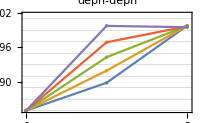
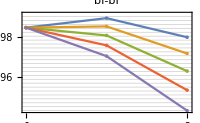
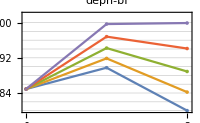
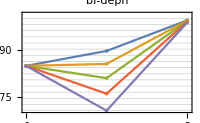

```mathematica
fidEnt=0.985; (* entanglement fidelity *)
dephfrac=Range[0,1,0.25];
fids=Association@Table[
methode->Association[#->Table[{round,DistFid[round,fidEnt,{1-#,#},methode]},{round,0,2}]&/@dephfrac]
,{methode,0,3}];
title=<|0->"deph-deph",1->"bf-bf",2->"deph-bf",3->"bf-deph"|>;
Row@Table[
minval=Min[Flatten[Values[fids[methode]],1][[All,2]]];
maxval=Max[Flatten[Values[fids[methode]],1][[All,2]]]+0.002;
Show[
ListPlot[Values@fids[methode],PlotLegends->Placed[Keys@fids[methode],Below],PlotLabel->title[methode]],ListPlot[Values@fids[methode],Joined->True],Ticks->{{0,1,2},Automatic},PlotRange->{{-0.01,2.02},{minval,maxval}},PlotLegends->Placed[Keys@fids[methode],Below],ImageSize->200,Frame->True,FrameTicks->{{0,1,2},Automatic},FrameStyle->Directive[Black,Thick],GridLines->{None,Range[minval,maxval,0.002]}
]
,{methode,{0,1,2,3}}]
```

Density matrix styling

```mathematica
chartstyle[label_]:={ImageSize->200,BarSpacing->0.1,ColorFunction->Function[{height},If[height<=10^-2,ColorData["DarkRainbow"][1+0.1*Log@height],ColorData["Pastel"][10*height]]],ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business",Ticks->{{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},{{1,"00"},{2,"01"},{3,"10"},{4,"11"}},Automatic},LabelStyle->Directive[Bold,Black],
Epilog->Inset[Style[label,Thick,17],ImageScaled[{.2,.7}]],PlotRange->{{1,4},{1,4},{0,0.5}}
};
```

```mathematica
chartbell[label_]:={ImageSize->200,BarSpacing->0.1,ColorFunction->Function[{height},ColorData["DarkRainbow"][height]],ChartElementFunction->"Cube",ChartStyle->EdgeForm[Thick],PlotTheme->"Business",Ticks->{{{1,"Φ+"},{2,"Φ-"},{3,"Ψ+"},{4,"Ψ-"}},{{1,"Φ+"},{2,"Φ-"},{3,"Ψ+"},{4,"Ψ-"}},Automatic},LabelStyle->Directive[Bold,FontFamily->"Helvetica"],
Epilog->Inset[Style[label,17,Bold],ImageScaled[{.3,.9}]],PlotRange->{{0.5,4.5},{0.5,4.5},{0,1}},
LabelingFunction->(Placed[Rotate[
Which[
#>=0.5,Style[NumberForm[#,5],13,GrayLevel[0.82]],
(#>=0.001)&&(#<=0.5),Style[NumberForm[#,4],10,Black],
True,Style[ScientificForm[#,2],10,Black]
]
,90 Degree],If[#1>=0.5,Center,Above]]&),
ViewAngle->All,
FaceGrids->None,Lighting->{{"Ambient", LightPurple}},
BoxRatios->{1,1,0.7},Axes->{True,True,False}
};
getcolor[height_]:=(If[10^-10<height<=10^-1,ColorData["Pastel"][1+0.1Log10@height],If[0<=height<=10^-10,White,ColorData["RoseColors"][height]]])
```

## Perfect distillation circuits with noisy remote entanglement

Bell basis transformation

```mathematica
mat2BellBasis[m_]:=With[
{p=(1/√2)*{{1,1,0,0},{0,0,1,-1},{0,0,1,1},{1,-1,0,0}},
pinv=(1/√2)*{{1,0,0,1},{1,0,0,-1},{0,1,1,0},{0,-1,1,0}}},
pinv.m.p]
```

```mathematica
?DistillationCircuit
```

```mathematica
DestroyAllQuregs[];
ρ6=CreateDensityQureg[6];
```

```mathematica
(**** Change the error fractions here for the raw entanglement ****)
ef={0,1};
entfid=0.96;
```

```mathematica
Options@Histogram3D
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BarOrigin→Bottom,BaselinePosition→Automatic,BaseStyle→{},Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ChartBaseStyle→Automatic,ChartElementFunction→Automatic,ChartElements→Automatic,ChartLabels→None,ChartLayout→Automatic,ChartLegends→None,ChartStyle→Automatic,ClipPlanes→None,ClipPlanesStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→False,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingFunction→Automatic,LabelStyle→{},LegendAppearance→Automatic,Lighting→Neutral,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→Automatic,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,ScalingFunctions→None,SphericalRegion→Automatic,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1}}

```mathematica
Print["raw to round 1"]
Row@{
ApplyCircuit[InitZeroState@ρ6,DistillationCircuit[0,entfid,ef,0]/.gatereplace];
PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,2,3,4,5]],Sequence@@chartbell["raw"]],
ApplyCircuit[InitZeroState@ρ6,DistillationCircuit[1,entfid,ef,0]/.gatereplace];
PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,2,3,4,5]],Sequence@@chartbell["deph"]],
ApplyCircuit[InitZeroState@ρ6,DistillationCircuit[1,entfid,ef,1]/.gatereplace];
PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,2,3,4,5]],Sequence@@chartbell["bf"]]}
```

raw to round 1

-Graphics3D--Graphics3D--Graphics3D-

```mathematica
Print["round 2"]
Row@{
While[Not@heraldout@ApplyCircuit[InitZeroState@ρ6,DistillationCircuit[2,entfid,ef,0]/.gatereplace]];
PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,2,3,4,5]],Sequence@@chartbell["deph-deph"]],
While[Not@heraldout@ApplyCircuit[InitZeroState@ρ6,DistillationCircuit[2,entfid,ef,2]/.gatereplace]];
PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,2,3,4,5]],Sequence@@chartbell["deph-bf"]],
While[Not@heraldout@ApplyCircuit[InitZeroState@ρ6,DistillationCircuit[2,entfid,ef,1]/.gatereplace]];
PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,2,3,4,5]],Sequence@@chartbell["bf-bf"]],
While[Not@heraldout@ApplyCircuit[InitZeroState@ρ6,DistillationCircuit[2,entfid,ef,3]/.gatereplace]];
PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,2,3,4,5]],Sequence@@chartbell["bf-deph"]]
}
```

round 2

-Graphics3D--Graphics3D--Graphics3D--Graphics3D-

## Zero, One, two-rounds of entanglement distillation on trapped ions

```mathematica
distcirc[p_,q_]:=<|
(*dephasing distillation sequence*)
0->Sequence@@{Subscript[Ry, p]["Alice",π/2],Subscript[Ry, p]["Bob",π/2],Subscript[CZ, p,q]["Alice"],Subscript[CZ, p,q]["Bob"],Subscript[Ry, q]["Alice",π/2],Subscript[Rx, p]["Alice",π],Subscript[Ry, q]["Bob",π/2]}
,
(*bitflip distillation sequence*)
1->Sequence@@{Subscript[Ry, q]["Alice",-π/2],Subscript[Ry, q]["Bob",-π/2],Subscript[CZ, p,q]["Alice"],Subscript[CZ, p,q]["Bob"],Subscript[Ry, q]["Alice",π/2],Subscript[Ry, q]["Bob",π/2]}
|>;

DistillationOnTrappedIons[nrounds_,device_,methode_]:=Module[{circ,seq},
(* raw entangled pairs *)
seq=<|
0->ConstantArray[0,nrounds],
1->ConstantArray[1,nrounds],
2->Table[If[OddQ[r],0,1],{r,nrounds}],
3->Table[If[OddQ[r],1,0],{r,nrounds}]
|>;
(* 3,3 *)
If[nrounds>=0,
circ={Subscript[Splz, 2,3]["Alice",4],Subscript[Splz, 2,3]["Bob",4],Subscript[Ent, 3,3]["Alice","Bob"]}
];
(* 3,3<>2,2->3,3 *)
If[nrounds>=1,
circ=Join[circ,{Subscript[Splz, 1,2]["Alice",2],Subscript[Splz, 1,2]["Bob",2],Subscript[Comb, 2,3]["Alice",2],Subscript[Comb, 2,3]["Bob",2],Subscript[SWAPLoc, 2,3]["Alice"],Subscript[SWAPLoc, 2,3]["Bob"],Subscript[Splz, 3,2]["Alice",4],Subscript[Splz, 3,2]["Bob",4],Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 3,2]["Alice",2],Subscript[Comb, 3,2]["Bob",2],distcirc[3,2][seq[methode][[1]]],Subscript[Splz, 3,2]["Alice",3],Subscript[Splz, 3,2]["Bob",3],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"]}]
];
(* 3,3<>3,3->3,3 store 3,3 to (1,1)   *)
If[nrounds>=2,
circ=Join[circ,{Subscript[Shutl, 2]["Alice",4],Subscript[Shutl, 2]["Bob",4],Subscript[Ent, 2,2]["Alice","Bob"],Subscript[Comb, 1,3]["Alice",1],Subscript[Comb, 1,3]["Bob",1],Subscript[SWAPLoc, 1,3]["Alice"],Subscript[SWAPLoc, 1,3]["Bob"],Subscript[Splz, 3,1]["Alice",3],Subscript[Splz, 3,1]["Bob",3],Subscript[Comb, 1,2]["Alice",3],Subscript[Comb, 1,2]["Bob",3],
Subscript[SWAPLoc, 1,2]["Alice"],Subscript[SWAPLoc, 1,2]["Bob"],Subscript[Splz, 2,1]["Alice",4],Subscript[Splz, 2,1]["Bob",4],Subscript[Ent, 1,1]["Alice","Bob"],Subscript[Comb, 2,1]["Alice",3],Subscript[Comb, 2,1]["Bob",3],
distcirc[2,1][seq[methode][[1]]],Subscript[Splz, 2,1]["Alice",2],Subscript[Splz, 2,1]["Bob",2],Subscript[Read, 1]["Alice"],Subscript[Read, 1]["Bob"],Subscript[Comb, 3,2]["Alice",2],Subscript[Comb, 3,2]["Bob",2],distcirc[3,2][seq[methode][[2]]],Subscript[Splz, 3,2]["Alice",1],Subscript[Splz, 3,2]["Bob",1],Subscript[Read, 2]["Alice"],Subscript[Read, 2]["Bob"]}];
];
circ
]
```

### Play around with the parameters

```mathematica
TIonDist::usage="TIonDist[device_options,ρ,nrounds,methode]. Distillation simulation on trapped ions.";
TIonDist[devoptions_,ρ_,nrounds_,methode_]:=Module[
{dev,circ,noisysch,noisycirc},
dev=TrappedIonOxford[Sequence@@devoptions];
circ=DistillationOnTrappedIons[nrounds,dev,methode];
noisysch=InsertCircuitNoise[CircTrappedIons[circ,dev,MapQubits->False],dev,ReplaceAliases->True];
noisycirc=ExtractCircuit@noisysch;
While[Not@heraldout@ApplyCircuit[ρ,noisycirc]];
noisysch
]
```

```mathematica
plotρ[label_]:=PlotDensityMatrix[Chop@mat2BellBasis[PartialTrace[ρ6,0,1,3,4]],Sequence@@chartbell[label]];
```

```mathematica
(** override the default parameters* *)
devoptions={
Nodes-><|"Alice"->3,"Bob"->3|>,
T1-><|"Alice"->3*10^9, "Bob"->3*10^9    |>,
T2s-><|"Alice"->10^5,  "Bob"->10^5   |>,
StdPassiveNoise->True,
DurMove-><|
"Alice"-> <|Shutl->25, Splz->50, Comb->50, SWAPLoc->10 |>,
"Bob"-><|Shutl->25, Splz->50, Comb->50, SWAPLoc->10 |>
|>,
FidInit-><|"Alice"->0.9999, "Bob"->0.9998|>,
DurInit-><|"Alice"->20,"Bob"->20|>,
DurRead-><|"Alice"->50, "Bob"->50|>,
BFProb-><|"Alice"->10^-3,"Bob"->10^-3|>,
ScatProb-><|"Alice"->0.05, "Bob"->0.05|>,
FidSingleXY-><|"Alice"->0.99999, "Bob"->0.99999|>,
EFSingleXY-><|"Alice"->{1,0},"Bob"->{1,0}|>,
RabiFreq-><|"Alice"->10, "Bob"->10 |>,
FreqCZ-><|"Alice"->0.1,"Bob"->0.1|>,
FidCZ-><|"Alice"->0.999, "Bob"->0.999|>,
EFCZ-><|"Alice"->{0.1,0.9},"Bob"->{0.1,0.9}|>,
FreqEnt->0.1,
FidEnt->0.95,
EFEnt->{0.1,0.9}
};
```

```mathematica
round1={
{TIonDist[devoptions,ρ6,0,0],plotρ["raw"]},
{TIonDist[devoptions,ρ6,1,0],plotρ["deph"]}
};
round2={
{TIonDist[devoptions,ρ6,2,0],plotρ["deph-deph"]},
{TIonDist[devoptions,ρ6,2,2],plotρ["deph-bf"]}};
```

```mathematica
round1[[All,2]]
round2[[All,2]]
```

{-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-}

```mathematica
round1[[All,2]]
round2[[All,2]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

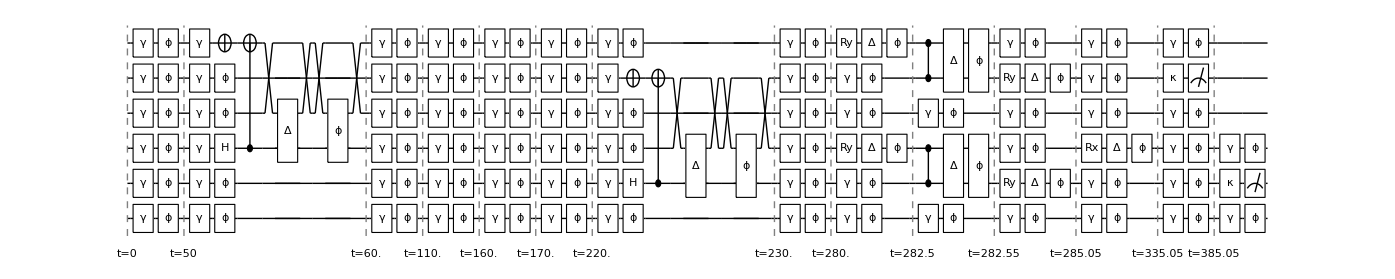

```mathematica
DrawCircuit[round1[[2,1]],6]
```

## Step-by-step distillation process + animation

```mathematica
(* Print distillation step by step *)
PrintDistillation[nrounds_,methode_,devoptions_]:=Module[
{dev,circ,ccirc,moves,show={}},
moves={Splz,Comb,SWAPLoc,Shutl};
dev=TrappedIonOxford[Sequence@@devoptions];
circ=DistillationOnTrappedIons[nrounds,dev,methode];
ccirc=CircTrappedIons[circ,dev,MapQubits->False];
AppendTo[show,{"initialise",dev[ShowNodes]}];
Table[
InsertCircuitNoise[ccirc[[c]],dev];
AppendTo[show,{StringRiffle[ToString[#,FormatType->StandardForm]&/@ccirc[[c]]],dev[ShowNodes]}]
,{c,Length@ccirc}];
show
]
```

```mathematica
AnimateDistillation::usage="AnimateDistillation[nrounds, methode, device_options]";
AnimateDistillation[nrounds_,methode_,devoptions_]:=Module[
{dev,circ,ccirc,moves,show={},format,noisy,fulltime,step=1},
format[zones_,noise_,t_,s_]:=Framed[Row@{Column[{"("<>ToString[s]<>") t="<>t<>"μs",Rasterize[zones,RasterSize->500,ImageSize->200]},Center],Pane[noise,280]}];
dev=TrappedIonOxford[Sequence@@devoptions];

(*move commands*)
moves={Splz,Comb,SWAPLoc,Shutl};
circ=DistillationOnTrappedIons[nrounds,dev,methode];
ccirc=CircTrappedIons[circ,dev,MapQubits->False];
 fulltime=ToString[N@#,FormatType->TraditionalForm]&/@(InsertCircuitNoise[ccirc,TrappedIonOxford[Sequence@@devoptions]][[All,1]]+OptionValue[TrappedIonOxford,DurInit]["Alice"]);
AppendTo[show,format[dev[ShowNodes],DrawCircuit[{Subscript[Init, #]&/@Range[0,5],Subscript[Damp, #][1.]&/@Range[0,5]}],"0",step++]];
Table[
noisy=InsertCircuitNoise[ccirc[[c]],dev];
AppendTo[show,
format[dev[ShowNodes],DrawCircuit[Flatten@noisy[[All,2]],dev[NumTotalQubits]],fulltime[[c]],step++]
]
,{c,Length@ccirc}];
show
]
```

```mathematica
(**   Render the steps into GIF animation   **)
picts = AnimateDistillation[2, 1, {Nodes -> <|"Alice" -> 3, "Bob" -> 3|>}];
Export["distillation.gif", picts, AnimationRepetitions -> 1, "DisplayDurations" -> ConstantArray[1, Length@picts], RasterSize ->600];
Import["distillation.gif", "AnimatedImage"]
```